# Arm state visualization

## Import

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
<<"PlotLegends`"

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_16__19_07_28"; (* range: 40 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__09_34_18";(* range: 50 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__13_32_26";(* range: 60 deg 2*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__12_20_59";(* range: 60 deg *)

 dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__00_17_05";(* range: 50 deg, 2 dist *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__00_34_50";(* range: 50 deg, 2 dist *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__17_06_21";(* range: 50 deg, 1 dist again*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_16__15_57_23";(* range: 50 deg *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_25__15_59_49"; (*  *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_25__16_00_05"; (* 0.781 *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__10_54_39";(* Long line: Inc. 0.82 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__12_51_07";(* Long line: 0.8823 *)
(*dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__12_51_33";(* Long line: 0.882 *)*)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_10_07__10_29_27";(* Long line: 0.748 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_10_07__15_58_20";(* Long line: 0.703 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_10_07__20_31_38";(* Long line: 0.703 *)

(* I4H6 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp4H6/13_10_09__20_48_16";(* Total KO: F0.81 !!! *)

(* I3H6 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_10__08_12_22";(* 0.8 KO: F0.82, large curvature at end *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_10__18_56_43";(* 0.8 KO, inc: F0.86, quite curved at end *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_11__08_47_14"; (* Total KO, inc: F0.877, still curved *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_14__17_48_53";(* Total KO, inc: F0.868, little curvature !*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_13__12_51_12";(* Total KO, inc: F0.868, original first run *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/ConMin/13_10_16__20_22_57";(* COnn mi.*)

(* I3H4 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H4/13_10_10__21_18_25";(* 0.8 KO: F0.76, works a little *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H4/13_10_11__00_52_23";(* 0.8 KO: F0.72, not very good *)


(* 2 positions *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_10_29__00_22_46";(* *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_10_26__12_11_44";(* *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_10_30__10_21_45";(* *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_10_30__20_46_43";(* *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_08__11_25_49";(* *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_11__09_20_31";(* inc1 *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_11__17_27_02";(* inc12 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_18__16_15_35";(* inc12 eval run, 50seconds*)


dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_12__10_19_09";(* inc13 +10 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_12__14_56_57";(* inc13 +10 deg *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_12__18_13_16";(* inc14 +0.1 s *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_13__11_46_58";(* inc142 +0.2 s *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_11__09_20_56";(* inc2  altern.*)

(* Min *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/Min/13_11_13__17_52_30";(* 5h, D0.8: 0.75 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/Min/13_11_15__10_08_47";(* 5h, D1.0: inc4 0.856 *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/Min/13_11_14__10_02_07"; (* 6h, D0.8: F0.724 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/Min/13_11_16__17_56_32"; (* 8h, D0.8: F0.71 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/Min/13_11_17__15_56_15"; (* 8h, D0.8: F0.72 *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/Min/H3/13_11_28__15_54_42"; (* 3h, D1.0: F0.827 *)

SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]]
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
avgfitness=Cases[fitXml,XMLElement["Generation",{_,_,"AverageFitness"->fit_},___]->fit,Infinity];
fitness=ToExpression[fitness];
avgfitness=ToExpression[avgfitness];
font="Arial";
```

{NeuralExtInput0,NeuralExtInput1,NeuralExtInput2,NeuralExtInput3,NeuralExtInput4,NeuralExtInput5,NeuralExtInput6,NeuralExtInput7,NeuralOutput0,NeuralOutput1,NeuralOutput2,NeuralOutput3,NeuralOutput4,NeuralOutput5,NeuralOutput6,NeuralOutput7,NeuralState0,NeuralState1,NeuralState2,NeuralState3,NeuralState4,NeuralState5,NeuralState6,NeuralState7,accelerationElbow,accelerationShoulder,angleElbow,angleShoulder,coriolisElbow,coriolisShoulder,dampingElbow,dampingShoulder,elbX,elbY,gravityElbow,gravityShoulder,inertiaElbow,inertiaShoulder,interactionElbow,interactionShoulder,lineX1,lineX2,lineY1,lineY2,torqueElbow,torqueShoulder,velocityElbow,velocityShoulder,x,y}

24000

## Config

```mathematica
plotOptions = {PlotRange->All};

numNeurons = Total[StringCount[varNames,"NeuralOutput"]]

dt =1/200;
T=12.0;
skip=0.0;
numTrials = Round[numData/(T/dt)];

SetTrial[trial_]:=Module[{},
t0=IntegerPart[1+(trial*T+skip)/dt];
tn= IntegerPart[t0+((T-skip)/dt)-1];
time=Range[tn-t0+1]*dt;
];

NtoI[name_]:=Position[varNames, name][[1,1]];

NtoDOld[name_]:=Table[data[[i,NtoI[name]]],{i,t0,tn}];
NtoD[name_]:=data[[t0;;tn,NtoI[name]]];

TimePlot[name_, options_, Scale_:1] := Module[{},
ListLinePlot[Transpose[{time,Scale*NtoD[name]}], Join[options,plotOptions]]
];

TimePlotT[name_, options_, tr_] := Module[{},SetTrial[tr];TimePlot[name,options,1]];

(*Inflate[x_,f_]:=If[x<0,(1+f)*)

XYPlot[tr_,name1_,name2_, options_] :=Module[{},
SetTrial[tr];
ListPlot[Transpose[{NtoD[name1],NtoD[name2]}], Join[options,plotOptions]]
];

XYPlotTime[tr_,name1_,name2_, options_]:=Module[{},
xy=XYPlot[tr,name1,name2,Join[options,{Joined->False}]]/.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.9*Range[0,1,1/Length[time]]]];
line = XYPlot[tr,name1,name2,Join[options,{Joined->True,PlotStyle->Red}]];
Show[line,xy]
];

MinExpand[x_,f_]:=If[x>=0,(1-f)*x,(1+f)*x];
MaxExpand[x_,f_]:=If[x>=0,(1+f)*x,(1-f)*x];

VarRange[v1_,v2_,f_,t0_:1,tn_:-1]:=Module[{d1,d2},
d1=data[[t0;;tn,NtoI[v1]]];
d2=data[[t0;;tn,NtoI[v2]]];
(*range={{MinExpand[Min[d1],f],MaxExpand[Max[d1],f]},{MinExpand[Min[d2],f],MaxExpand[Max[d2],f]}}*)
range = VarRangeD[d1,d2,f,t0,tn]
 ];

VarRangeD[d1_,d2_,f_,t0_:1,tn_:-1]:=Module[{},
range={{MinExpand[Min[d1],f],MaxExpand[Max[d1],f]},{MinExpand[Min[d2],f],MaxExpand[Max[d2],f]}}
 ];

PartitionOdd[l_]:=If[EvenQ[Length[l]],Partition[l,2],Partition[l,2,2,{1,1},Null]];

PlotEnvLine[t_,options_]:=Module[{x1i,x2i,y1i,y2i,x1,x2,y1,y2},
SetTrial[t];
x1i=NtoI["lineX1"];
x2i=NtoI["lineX2"];
y1i=NtoI["lineY1"];
y2i=NtoI["lineY2"];
x1 = data[[t0,x1i]];
x2 = data[[t0,x2i]];
y1 = data[[t0,y1i]];
y2 = data[[t0,y2i]];
ListLinePlot[{{x1,y1},{x2,y2}}, Join[options,plotOptions]]
];


le=0.32;
ls=0.33;
armLength =le+ls;
elb=1;
InvKin[xi_, yi_]:=Module[{x,y,d,ae,t1,t2,xx,yy},
(* First clamp to arm length *)
d=Sqrt[xi^2+yi^2];
x=If[d>armLength,(xi/d)*armLength,xi];
y=If[d>armLength,(yi/d)*armLength,yi];

ae=x^2+y^2-le^2-ls^2;
ae/=2.0*le*ls;
ae=elb*Abs[ArcCos[ae]];

t1=ls+le*Cos[ae];
t2=le*Sin[ae];
xx=x*t1+y*t2;
yy=y*t1-x*t2;
as=ArcTan[xx,yy];
angles={ae,as}
];

InvKinP[p_]:=InvKin[ p[[1]],p[[2]] ];

IntPolLine[x1_,y1_,x2_,y2_,n_]:=Module[{l},
l=Range[0,1,1/n];
x=x1+l*(x2-x1);
y=y1+l*(y2-y1);
xy=Transpose[{x,y}]
];

SetTrial[0];
```

8

## Fitness

{3000}

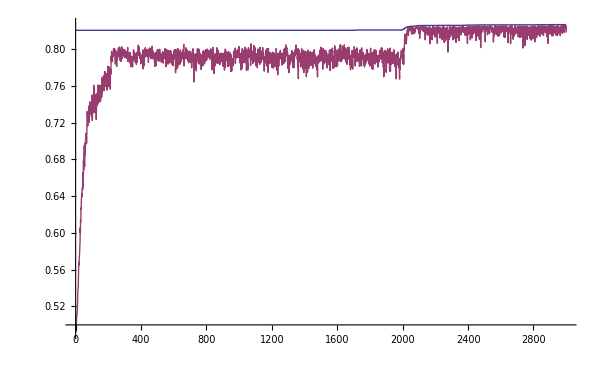

0.826611

```mathematica
Dimensions[fitness]

fit={fitness,avgfitness};
fitP =ListLinePlot[fit,PlotRange->All,ImageSize->600]
maxFit = Max[fitness]
```

## Generalization

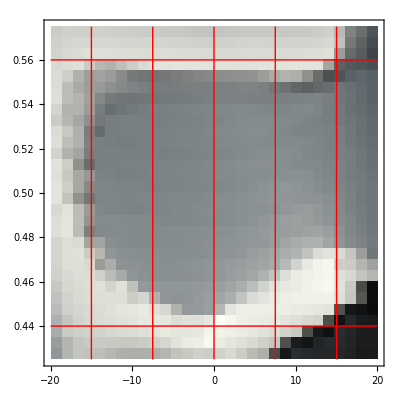
-Graphics--Graphics-

```mathematica
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_14__18_50_33";(* test run of 17_27_02: 20x20 trials *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H3/EvalRuns/13_12_02__16_46_16";(* test run of H3: 30x30 trials *)

SetDirectory[dirName];

genFit=Import["Fitness.txt","Table"];
genFit=genFit[[2;;-2,1]];
trialspervar=Sqrt[Length[genFit]];
genFitMin=Min[genFit];
genFitMax=Max[genFit];
genFit = Partition[genFit,trialspervar];

color="GrayTones";
ColorData[color];
colorScaling=False;
colorFunc=ColorData[color]@Rescale[#,{genFitMin,genFitMax},{0,1}]&;

Colorbar[colorFunction_: Automatic,min_:0,max_:1,divs_: 25]:=DensityPlot[y,{x,0,1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,FrameTicks->{None,Automatic,None,None},ColorFunction->colorFunction,ColorFunctionScaling->colorScaling];

drange={{-20,20},{0.425,0.575}};
grid={Range[-15,15,7.5],Range[0.44,0.65,0.12]};

fitdens=ReliefPlot[genFit,ColorFunctionScaling->colorScaling,ColorFunction->colorFunc,DataRange->drange,AspectRatio->1,PlotRange->All,FrameTicks->True,Mesh->grid,MeshStyle->Red];

fitDensityPlot=With[{size=350},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{fitdens,Colorbar[colorFunc,genFitMin,genFitMax,5]}]];
fitpl=fitDensityPlot
```

### First contact

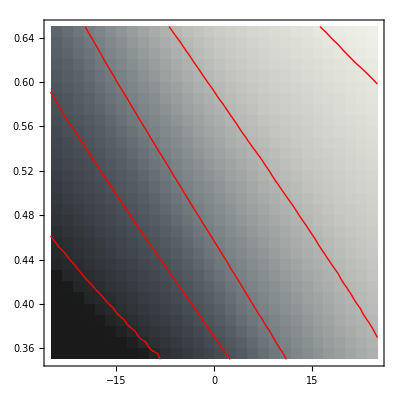
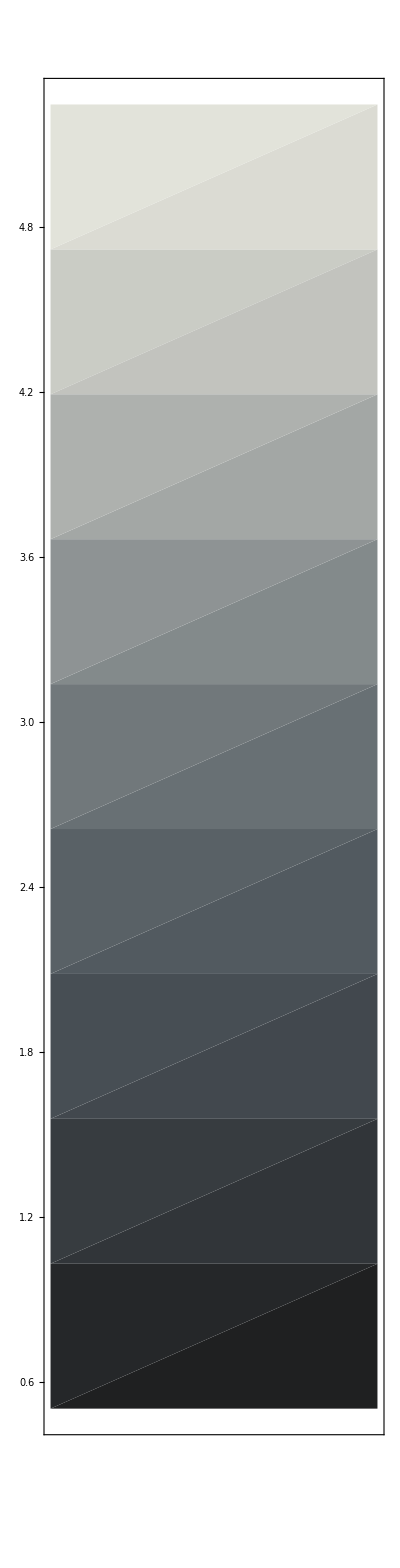

```mathematica
(* Contacts *)
contacts=Import["FirstContacts.txt","Table"];
contactTimes=contacts[[All,1]];
conMin=Min[contactTimes];
conMax=Max[contactTimes];
contactTimesMat=Partition[contactTimes,trialspervar];
colorFunc=ColorData[color]@Rescale[#,{conMin,conMax},{0,1}]&;

conDens=ReliefPlot[contactTimesMat,ColorFunctionScaling->colorScaling,ColorFunction->colorFunc,DataRange->{{-25,25},{0.35,0.65}},AspectRatio->1,PlotRange->All,FrameTicks->True];
conCont=ListContourPlot[contactTimesMat,DataRange->{{-25,25},{0.35,0.65}},ContourLines->True,ContourStyle->Red,ContourShading->None];
conts=Show[conDens,conCont];

conDensPlot=With[{size=350},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{conts,Colorbar[colorFunc,conMin,conMax,10]}]];
conpl=conDensPlot
```

```mathematica
(* Joint angles at sensor blackout... *)
(*dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_19__17_21_33";(* test run of 17_27_02: 10x10 trials *)
SetDirectory[dirName];
bigData=Import["State.txt", "Table"];
states = bigData[[2;;-2]];
Dimensions[states]
*)
```

```mathematica
(*
Clear[a];Clear[a2];Clear[PlotAnglesAt];
tx=8/dt;
skip=0;
m=Length[states];
mtr=T/dt;
numEvals = Round[m/(T/dt)];

(* Angles at specific time index for single given trial *)
AnglesAt[tr_,ti_,mtr_]:=Module[{ie,is,i,a},
ie=NtoI["angleElbow"];
is=NtoI["angleShoulder"];
i=-1+(tr*mtr)+ti; (* -1: compatibilty with SetTrial ?! *)
a={states[[i,ie]],states[[i,is]]}
];

(* Matrix of joint angles. One row per line position, one column per line angles  *)
AllAnglesAt[ti_,mtr_,c_:1,th_:0]:=Module[{a},
a=Table[AnglesAt[i,ti,mtr],{i,0,numEvals-1}];
Print["xlim: ",Min[a[[All,1]] ]," ",Max[a[[All,1]] ]];
Print["ylim: ",Min[a[[All,2]] ]," ",Max[a[[All,2]] ]];
a=Partition[a,10]; (* One row per varying line positions, i.e. 10 rows of 10 line angles each *)
(* Find all angles where the first angle is smaller than a threshold *)
a=DeleteCases[a,_?(#[[c]]<th&),2,Infinity]
];

Options[PlotAnglesAt]={PlotMarkers->{Automatic,8}};

PlotAnglesAt[a_,r_,opts:OptionsPattern[]]:=
Show[Table[If[Length[ a[[i]] ]>0,ListLinePlot[ a[[i]] ,Joined->True,PlotStyle->Directive[Gray,Opacity->i/i],PlotRange->r,AxesOrigin->{r[[1,1]],r[[2,1]]},AxesLabel->{"elbow","shoulder"},Evaluate@FilterRules[{opts,Options[PlotAnglesAt]},Options@ListLinePlot]],{}],{i,1,Length[a]}]];


range={{0.9,1.7},{-0.5,-0.12}};
origin={range[[1,1]],range[[2,1]]};


ang=AllAnglesAt[tx,mtr,1,0.9];
pla8=PlotAnglesAt[ang,{{1.0,1.6},{-0.5,-0.1}}];

ang2=AllAnglesAt[6/dt,mtr,1,1];
pla6=PlotAnglesAt[ang2,{{1,1.7},{-1,-0.5}}];
GraphicsRow[{pla6,pla8},ImageSize->800]
*)
```

```mathematica
(* Joint angles at initial sensor contact *)
(*contacts=Flatten[Import["Contacts.txt","Table"]];
conMin=Min[contacts];
conMax=Max[contacts];
initAng=Table[AnglesAt[i-1,Round[contacts[[i]]/dt],mtr],{i,1,numEvals}];
*)
(*initAngMat=Partition[initAng,10];
outlierPos=Position[initAngMat,_?(#[[1]]>1.2&&#[[2]]>-1&),2,Infinity];
initAngMatRed=DeleteCases[initAngMat,_?(#[[1]]>1.2&&#[[2]]>-1&),2,Infinity];
plaInit=PlotAnglesAt[initAngMatRed,{{0.6,1.9},{-1.3,-0.68}}]*)
```

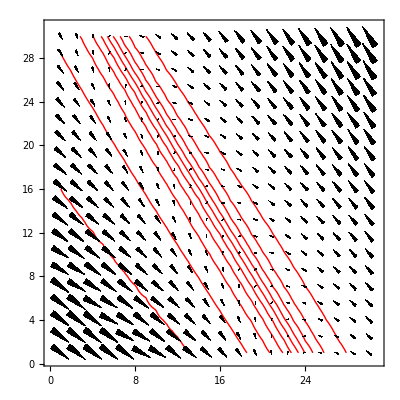

```mathematica
(* Used for vector field *)
contactAngs=contacts[[1;;-1,2;;3]];
standAng=Standardize[contactAngs];
standAngMat=Partition[standAng,trialspervar];
(*standAngMat=ReplacePart[standAngMat,outlierPos->{0,0}]; (* Remove unsuccessful outliers *)*)

(* 1d Angle from 2d vector *)
VecToAng[v_]:=ArcTan@@Normalize[v];
TwoPi[a_]:=If[a<0,a+2Pi,a];

angRed=Map[VecToAng,standAng];
angRedMat=Partition[angRed,trialspervar];

angRedCor=Map[TwoPi,angRed];
angRedCorMat=Partition[angRedCor,trialspervar];
(*angRedCorMat=ReplacePart[angRedCorMat,outlierPos->None](* Remove unsuccessful outliers *)*)
(*angMatPl=ReliefPlot[angRedCorMat,ColorFunctionScaling->True,ColorFunction->ColorData["GrayTones"],AspectRatio->1,PlotRange->Automatic,FrameTicks->True,ImageSize->400];*)

prange=drange;

angContPl=ListContourPlot[angRedCorMat,ContourShading->None,ColorFunction-> ColorData["ValentineTones"],ColorFunctionScaling->True,InterpolationOrder->1,Contours->10,ContourStyle->{{Red,Thick}}];

vecPl=ListVectorPlot[Transpose[standAngMat],VectorPoints->20,VectorScale->Automatic,VectorStyle->{Black,"Pointer"}];

Show[angContPl,vecPl,PlotRange->All]
```

### Angles at last contact

```mathematica
(*
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/SingleRuns/SameLastContact/13_11_22__11_29_16";(* test run of 17_27_02: 100x100. p0.5, 90.ba *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/SingleRuns/SameLastContact/13_11_22__11_30_18";(* test run of 17_27_02: 100x100. p0.45, 95.ba *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/SingleRuns/SameLastContact/13_11_22__11_31_44";(* test run of 17_27_02: 100x100. p0.5, 90.ba, >var *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/SingleRuns/SameLastContact/13_11_22__11_34_19";(* test run of 17_27_02: 100x100. p0.5, 90.ba, >>var *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/SingleRuns/SameLastContact/13_11_28__12_18_04";(* test run of 17_27_02: 100x100. p0.45+-0.05, 90.ba *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/SingleRuns/SameLastContact/13_11_28__13_06_30";(* test run of 17_27_02: 25x25. p0.475+-0.025, 90.ba *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/SingleRuns/SameLastContact/13_11_28__16_27_14";(* test run of 17_27_02: 30x30. p0.47+-0.025, 85.ba *)
SetDirectory[dirName];
*)

anglesAndLineConf=Import["LastContacts.txt", "Table"];
contAng=anglesAndLineConf[[1;;-1,1;;2]];
lineConf=anglesAndLineConf[[1;;-1,3;;4]];
fitness = Import["Fitness.txt","Table"][[2;;-2,1]];
fitMat=Partition[fitness,trialspervar];
outlierPos=Position[fitMat,_?(#<0.6&),2,Infinity];
(*MatrixForm[fitness]*)
```

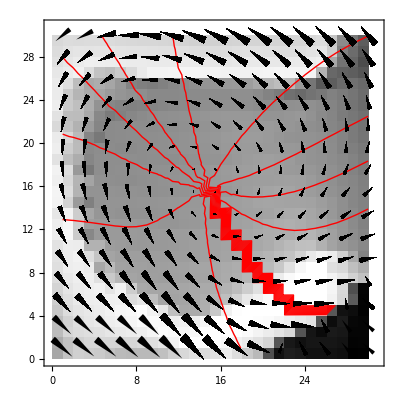

```mathematica
contAngSt=Standardize[contAng];
contAngStMat=Partition[contAngSt,trialspervar];
(contAngStMat[[##]]=Normalize[contAngStMat[[##]]])&@@@outlierPos; (* Fuck me! It works, but noone will ever understand it... *)
(*contAngStMat=ReplacePart[contAngStMat,outlierPos->{0,0}];(* Remove unsuccessful outliers *)*)

contAngRed=Map[TwoPi,Map[VecToAng,contAngSt]];
contAngRedMat=Partition[contAngRed,trialspervar];
contAngRedMat=ReplacePart[contAngRedMat,outlierPos->None];(* Remove unsuccessful outliers *)

(*angMatPl=ReliefPlot[contAngRedMat,ColorFunctionScaling->True,ColorFunction->ColorData["GrayTones"],AspectRatio->1,PlotRange->Automatic,FrameTicks->True,ImageSize->400]*)
fitnessPl=ReliefPlot[fitMat,ColorFunctionScaling->True,ColorFunction->GrayLevel,AspectRatio->1,FrameTicks->True,ImageSize->400];
contAngConPl=ListContourPlot[contAngRedMat,ContourShading->None,ColorFunction-> ColorData["ValentineTones"],ColorFunctionScaling->True,InterpolationOrder->1,Contours->10,ContourStyle->{{Red,Thick}}];
contAngVecPl=ListVectorPlot[Transpose[contAngStMat],VectorStyle->{Black,"Pointer"}];
Show[fitnessPl,contAngConPl,contAngVecPl]
```

### Angles at last contact in joint space (higher res)

Fitness range: 0.497753 0.867591

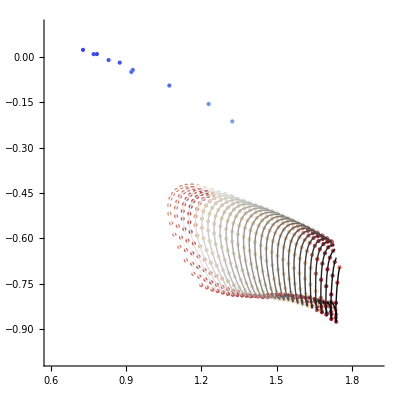

```mathematica
(* sub-sample from 10.000 to 1000 or so *)
nth=2;
fitSub=fitness[[1;;-1;;nth]];
fitMat=Partition[fitness,trialspervar];
outliers=Position[fitSub,_?(#<0.6&),1,Infinity];
outliersMat=Position[fitMat,_?(#<0.6&),2,Infinity];
minFit=Min[fitSub];
maxFit=Max[fitSub];
Print["Fitness range: ",minFit, " ",maxFit]

range={{0.6,1.9},{-1,0.1}};

ScaleMM[x_,min_,max_]:=(x-min)/(max-min);

contAngSub=contAng[[1;;-1;;nth]];
(*contAngSub=ReplacePart[contAngSub,outliers->{}];*)
scatter=Table[Graphics[{ColorData["ThermometerColors"][ScaleMM[fitSub[[i]],minFit,maxFit]],PointSize[Medium],Point[contAngSub[[i]]]}],{i,1,Length[contAngSub]}];
scatterPl=Show[scatter,Axes->True,PlotRange->range,AspectRatio->1];

contAngMat=Partition[contAng,trialspervar];
contAngMat=Delete[contAngMat,outliersMat];

Options[PlotAnglesAt]={PlotMarkers->{Automatic,8}};
PlotAnglesAt[a_,r_,opts:OptionsPattern[]]:=
Show[Table[If[Length[ a[[i]] ]>0,ListLinePlot[ a[[i]] ,Joined->True,PlotStyle->Directive[GrayLevel[i/Length[a]]],PlotRange->r,AxesOrigin->{r[[1,1]],r[[2,1]]},AxesLabel->{"elbow","shoulder"},Evaluate@FilterRules[{opts,Options[PlotAnglesAt]},Options@ListLinePlot]],{}],{i,1,Length[a]}]];

linePl=PlotAnglesAt[contAngMat,range,PlotMarkers->None];
Show[scatterPl,linePl,ImageSize->400]
```

```mathematica
(* Find equal poses *)
AllPairs[a_,cond_]:=Select[Subsets[a,{2}],cond@@#&];
res=AllPairs[contAng, SquaredEuclideanDistance[#1,#2]<0.0000001&];
res=Flatten[res,1];
pos=Flatten[Table[Position[contAng,res[[i]]],{i,1,Length[res]}]]
fitness[[pos]]
```

{1,46,242,243}

{0.723191,0.861222,0.822899,0.835525}

```mathematica
sel=0;
sel1=sel*2+1;
sel2=sel*2+2;
contAng[[pos[[sel1]]]]
contAng[[pos[[sel2]]]]

lineConf[[pos[[sel1]]]]
lineConf[[pos[[sel2]]]]

fitness[[pos[[sel1]] ]]
fitness[[pos[[sel2]] ]]
```

{1.47183,-0.412129}

{1.47182,-0.412072}

{0.445,83.7931}

{0.460517,89.6552}

0.818753

0.813479

## Figures

### Cartesian Space

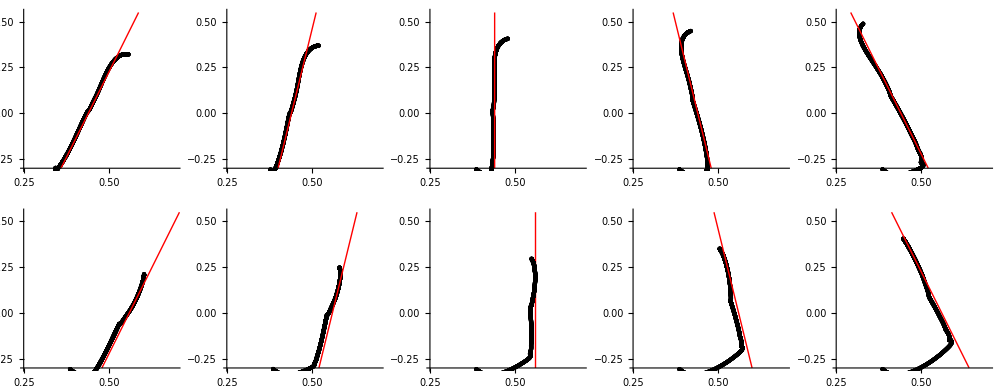

```mathematica
(*Map[GrayLevel,NtoD["NeuralOutput0"]]*)
skip = 2;
range ={{0.25,0.7},{-0.3,0.55}};
origin={range[[1,1]],range[[2,1]]};
PlotLineTraj[t_,options_:{}]:=Module[{p1,p2,r,o},
SetTrial[t];
(*r=VarRange["x","y",0.1,IntegerPart[t0],IntegerPart[tn]];*)
(*o={r[[1,1]],r[[2,1]]};*)
r=range;
o=origin;
p1=XYPlot[t,"x","y",Join[options,{PlotRange->r,PlotStyle->{Black},AxesOrigin->o}]] /.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.8-0.8*NtoD["NeuralOutput0"]]];
p2= PlotEnvLine[t,Join[options,{PlotRange->r,PlotStyle->{Red}}]];
Show[p1,p2]
];

If[numTrials ≤ 5,
GraphicsRow[Table[PlotLineTraj[i,{AspectRatio->1}],{i,0,4}],ImageSize->800],
GraphicsGrid[Table[PlotLineTraj[i*(numTrials/2)+j,{AspectRatio->1}],{i,0,1},{j,0,-1+numTrials/2}],ImageSize->1000]]
```

### Joint space trajectories

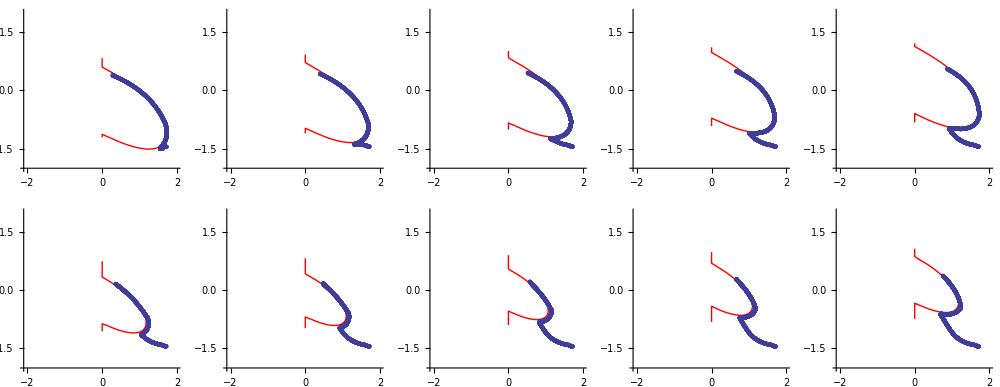

```mathematica
skip=1;
trial = 0;
SetTrial[trial];

PlotAngTraj[tr_,des_:1]:=Module[{x1,y1,x2,y2,xy,angIntp,angIntPlot,angActPl, angActPl2,range,origin},
SetTrial[tr];
x1=NtoD["lineX1"][[1]];
y1=NtoD["lineY1"][[1]];
x2=NtoD["lineX2"][[1]];
y2=NtoD["lineY2"][[1]];
xy = IntPolLine[x1,y1,x2,y2,100];
angIntp = Map[InvKinP,xy];

angIntPlot=ListPlot[angIntp,Joined->True,PlotStyle->Red]/.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.8*Range[0,1,1/100]]];

angActPl=XYPlot[tr,"angleElbow","angleShoulder",{PlotStyle->Black,Joined->True}];
angActPl2=XYPlot[tr,"angleElbow","angleShoulder",{}]/.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.8-0.8*NtoD["NeuralOutput0"] ]];

(* get maximum range of line and actual joint trajectory *)
(*range=VarRangeD[ Join[angIntp[[All,1]],NtoD["angleElbow"]],Join[angIntp[[All,2]],NtoD["angleShoulder"]],0.1 ];*)
range={{-2.1,2},{-2,2}};
origin={range[[1,1]],range[[2,1]]};
Show[If[des≠0,angIntPlot,{}],angActPl,angActPl2,PlotRange->range,AxesOrigin->origin,AspectRatio->1]
];

If[numTrials ≤ 5,
GraphicsRow[Table[PlotAngTraj[i],{i,0,numTrials-1}],ImageSize->1000],
GraphicsGrid[Table[PlotAngTraj[i*(numTrials/2)+j],{i,0,1},{j,0,-1+numTrials/2}],ImageSize->1000]]
```

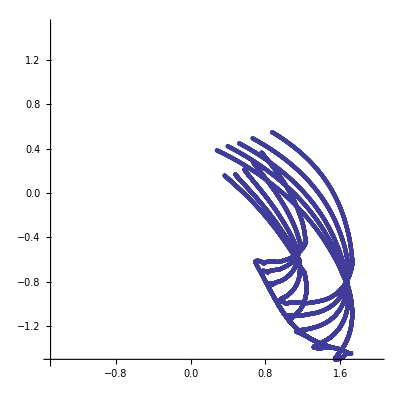

```mathematica
skip=1;
range={{-1.5,2},{-1.5,1.5}};
origin={range[[1,1]],range[[2,1]]};
Show[Table[PlotAngTraj[i,0],{i,numTrials-1,0,-1}],ImageSize->400,PlotRange->range,AxesOrigin->origin]
```

### Neural time trace

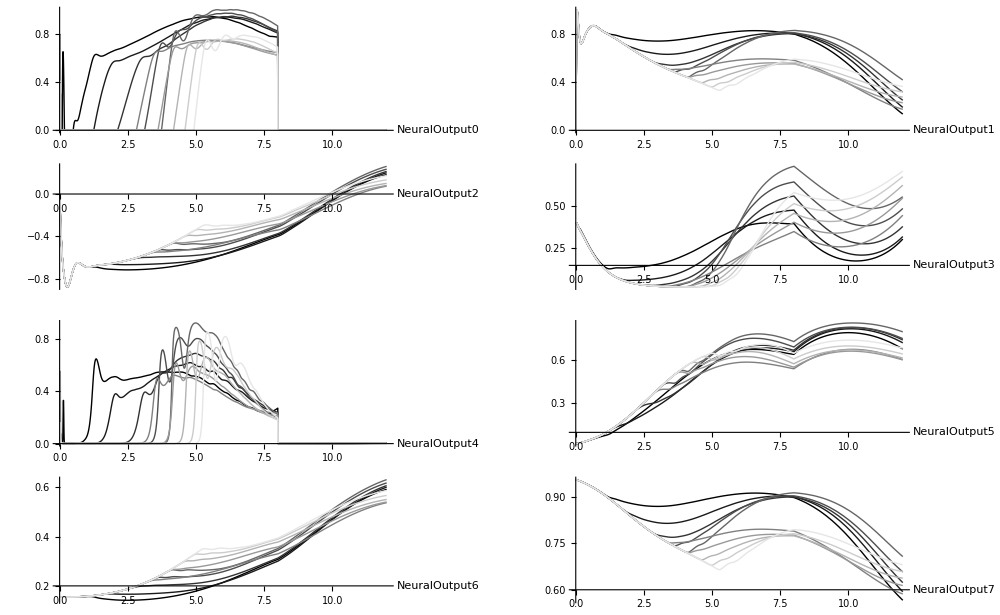

```mathematica
size=1000;
skip=0;

PlotAllTrials[var_]:=Show[Table[TimePlotT[var,{PlotStyle->GrayLevel[i/numTrials],PlotRange->{All,All},AspectRatio->0.3,AxesLabel->{var,""},ImageSize->size,ImagePadding->{{20,0},{20,10}}},i],{i,0,numTrials-1}],ImageSize->size];

GraphicsGrid[
PartitionOdd[Table[PlotAllTrials["NeuralOutput"<>ToString[i]],{i,0,numNeurons-1}]],ImageSize->size]
```

### Strobe

```mathematica
skip=1;
strobeVars={"NeuralOutput3","NeuralOutput1","NeuralOutput2"};
strobeVars2={"NeuralOutput5","NeuralOutput1","NeuralOutput2"};
strobeColors={Magenta,Green,Red};
strobeTimes={3-skip,6-skip,8-skip};

(* Extract strobes for given trial at single point in time *)
Strobe[tr_,vars_,t_]:=Module[{x,y,z},
SetTrial[tr];
x=NtoD[vars[[1]]];
x=x[[t/dt]];
y=NtoD[vars[[2]]];
y=y[[t/dt]];
z=NtoD[vars[[3]]];
z=z[[t/dt]];
pos={x,y,z}
];

(* Get strobes for all trials at a single point in time *)
Strobes[vars_,t_]:=Table[Strobe[i,vars,t],{i,0,numTrials-1}];

(* Plot a 3d trajectory *)
Plot3d[tr_,vars_]:=Module[{traj,op,vc},
SetTrial[tr];
traj=Transpose[{NtoD[vars[[1]]],NtoD[vars[[2]]],NtoD[vars[[3]]]}];
op=NtoD["NeuralOutput0"];
vc=If[tr<5,(RGBColor[0,0,0,0.3+0.7*#])&/@op,(RGBColor[0,0,1,0.3+0.7*#])&/@op];
pl=Graphics3D[{Thick,Line[traj,VertexColors->vc]},PlotRange->All,Boxed->True,BoxStyle->{LightGray},Axes->True,BoxRatios->1]
];

(* Plot trajectories for all trials, and strobes at several points in time *)
StrobePlot[vars_,times_]:=Module[{numStrobes,strobes, scatters, lines,plot},
numStrobes=Length[times];
strobes=Table[Strobes[vars,strobeTimes[[i]]],{i,1,numStrobes}];
scatters=Table[Graphics3D[{strobeColors[[i]],PointSize[Large],Point[strobes[[i]]]}],{i,1,numStrobes}];
lines=Show[Table[Plot3d[i,vars],{i,numTrials-1,0,-1}]];
plot=Show[lines,Show[scatters]]
]

(* Final plot with chosen viewing angle *)
sp1=Show[StrobePlot[strobeVars,strobeTimes],ViewPoint->{-1.5,-0.2,0.4},AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->strobeVars];
sp2=Show[StrobePlot[strobeVars2,strobeTimes],ViewPoint->{-1.5,-0.2,0.4},AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->strobeVars2];
GraphicsRow[{sp1,sp2},ImageSize->800]
```

-Graphics-

```mathematica
Show[sp1,ViewPoint->{-1.5,-0.8,0.4},AxesEdge->{{-1,-1},{-1,-1},{1,-1}}]
```

-Graphics3D-

### First contact

{1.97}

{1.97,2.925,3.41,3.195,3.62}

{3.72,4.195,4.21,4.55,4.82}

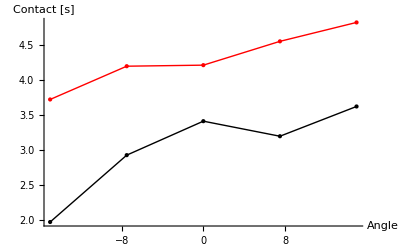

```mathematica
skip = 0.5; (* Discard transient contacts in initial period *)
threshold=0.7;

SetTrial[0];
sensor=NtoD["NeuralOutput0"];

FirstContact[tr_]:=Module[{i},
SetTrial[tr];
sensor=NtoD["NeuralOutput0"];
(*i=Flatten[Position[sensor,1.0,1,1]];
tp=time[[i]]//N *)
i=Flatten[Position[sensor,_?(#>threshold&),1,1]];
tp=time[[i]]//N
]

tp=FirstContact[0]
lp1=Flatten[Table[FirstContact[i],{i,0,4}]]
lp2=Flatten[Table[FirstContact[i],{i,5,9}]]
angles={-15,-7.5,0,7.5,15};
joined=True;
lp1Pl=ListLinePlot[Transpose[{angles,lp1}],PlotStyle->Black,Joined->joined];
lp1Pl2=ListLinePlot[Transpose[{angles,lp1}],PlotStyle->Black,Joined->!joined];
lp2Pl=ListLinePlot[Transpose[{angles,lp2}],PlotStyle->Red,Joined->joined];
lp2Pl2=ListLinePlot[Transpose[{angles,lp2}],PlotStyle->Red,Joined->!joined];
Show[lp1Pl,lp1Pl2,lp2Pl,lp2Pl2,AxesLabel->{"Angle","Contact [s]"},PlotRange->{{-15,15},Automatic},AxesOrigin->{-15,0}]
```